```mathematica
(*
This file generate Ellipses which are invariante under translation, rescaling and rotation.
This is to be used to generate data for shape clustering.
*)
```

```mathematica
X[a_,θ_]:=a Cos[θ]
Y[b_,θ_]:=b Sin[θ]
X0:= RandomReal[{-5,5}]
Y0:=RandomReal[{-5,5}]
R[α_]:={{Cos[α], -Sin[α]},{Sin[α], Cos[α]}}

MyEllipse[x0_,y0_,a_,b_,α_,s_,n_]:=(
angles = Table[2*Pi*i/n//N,{i,1,n}];
points = Table[
s*(R[α].{X[a,angles[[i]]],Y[b,angles[[i]]]})+{x0,y0}, 
{i,1,n}
];
Return[points];
)

Cluster[n_,m_,a_,b_]:=(
(* 
	n: number of data points,
	m: number of landmark points,
	a, b: semi-axis of the ellipse
 *)
x=Table[
MyEllipse[X0,Y0,a,b,RandomReal[{0,2*Pi}],RandomReal[{0.5,5}],m],
{i,1,n}
];
Return[x];
)
```

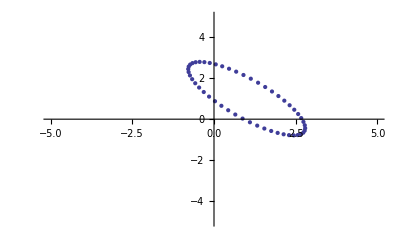

```mathematica
ListPlot[MyEllipse[1,1,1,3,Pi/4,0.8,50],PlotRange->{{-5,5},{-5,5}}]
```

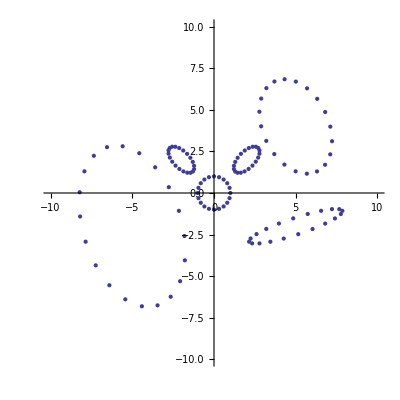

```mathematica
Show[{
ListPlot[MyEllipse[0,0,1,1,0,1,20]],
ListPlot[MyEllipse[2,2,1,.5,Pi/4,1,20]],
ListPlot[MyEllipse[-2,2,.5,1,Pi/4,1,20]],
ListPlot[MyEllipse[5,4,2,3,Pi/7,1,20]],
ListPlot[MyEllipse[-5,-2,3,5,Pi/10,1,20]],
ListPlot[MyEllipse[5,-2,3,.5,Pi/10,1,20]]
},
AspectRatio->1,
PlotRange->{{-10,10},{-10,10}}
]
```

```mathematica
MyEllipse[5,5,1,1.5,Pi/4,20]//MatrixForm
```

(5.34474 | 6.00026
4.94862 | 6.1955
4.55753 | 6.27372
4.20976 | 6.22726
3.93934 | 6.06066
3.77274 | 5.79024
3.72628 | 5.44247
3.8045 | 5.05138
3.99974 | 4.65526
4.29289 | 4.29289
4.65526 | 3.99974
5.05138 | 3.8045
5.44247 | 3.72628
5.79024 | 3.77274
6.06066 | 3.93934
6.22726 | 4.20976
6.27372 | 4.55753
6.1955 | 4.94862
6.00026 | 5.34474
5.70711 | 5.70711)

```mathematica
x=Cluster[10,10,1,1.5];
```

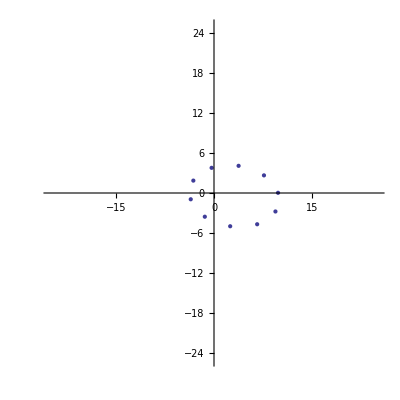
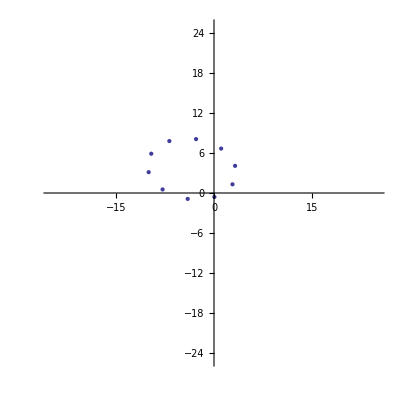
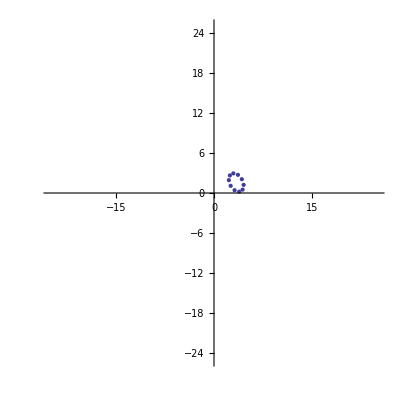
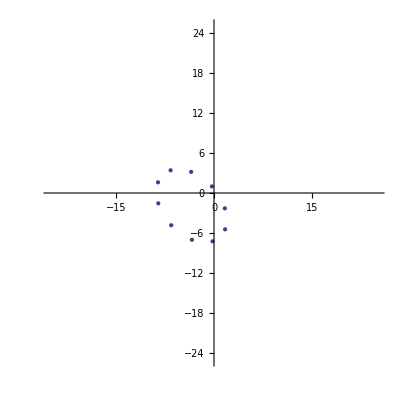
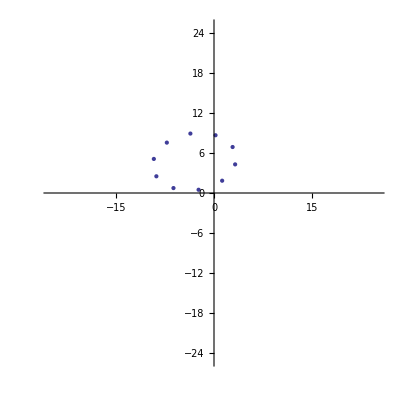
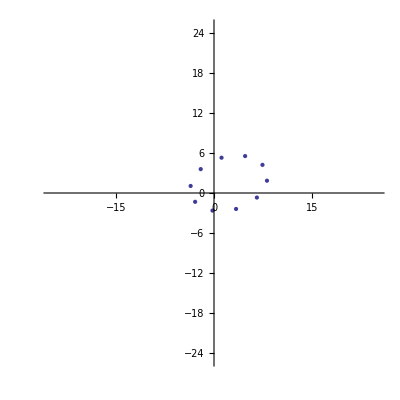
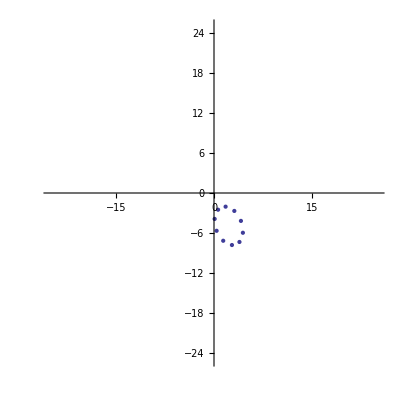
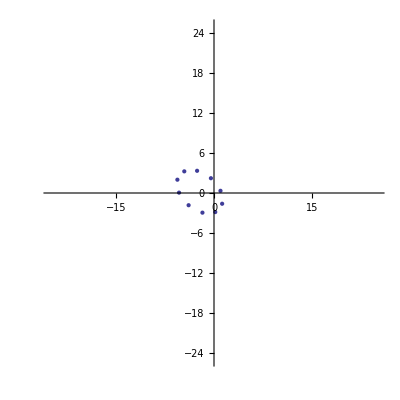

```mathematica
Table[ListPlot[x[[i]],PlotRange->{{-25,25},{-25,25}},AspectRatio->1],{i,1,Length[x]}]
```

```mathematica
Manipulate[
(
x1=Cluster[10,20,a,b];
Table[ListPlot[x1[[i]],PlotRange->{{-15,15},{-15,15}},AspectRatio->1],{i,1,Length[x]}]
)
,{a,0.1,2},{b,0.1,2}]
```

```mathematica
data=Cluster[30,20,2,4];
```

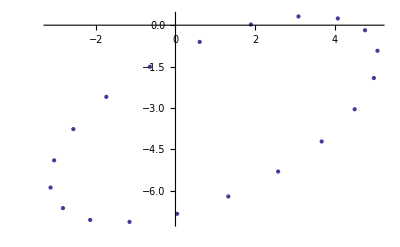
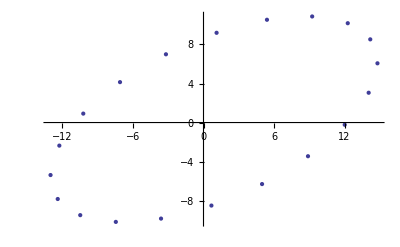
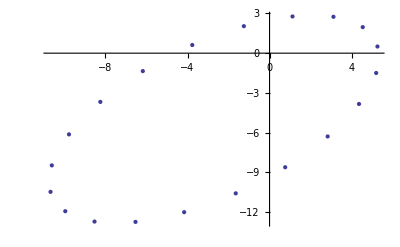
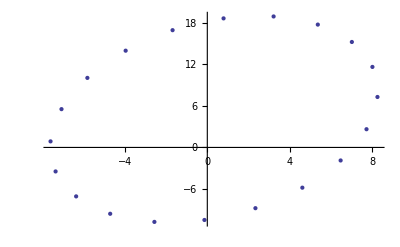
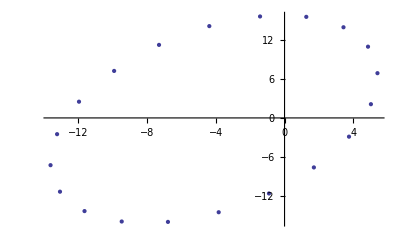
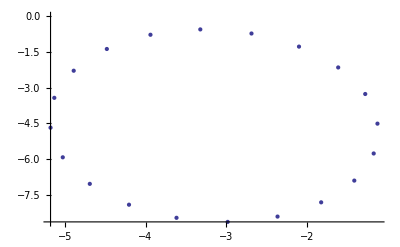
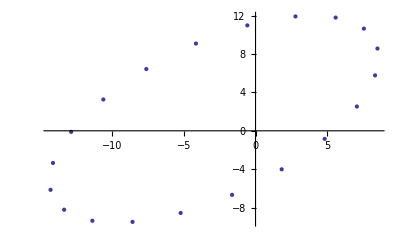
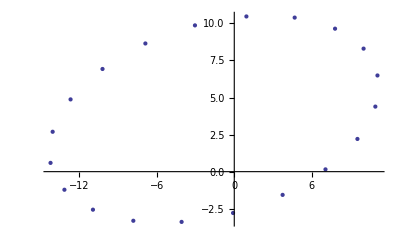

```mathematica
Table[ListPlot[data[[i]]],{i,1,Length[data]}]
```

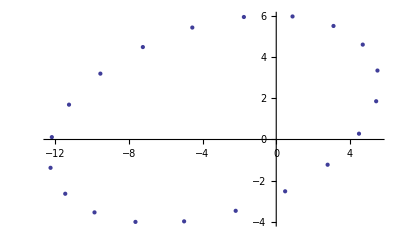
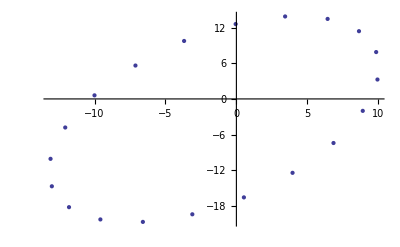
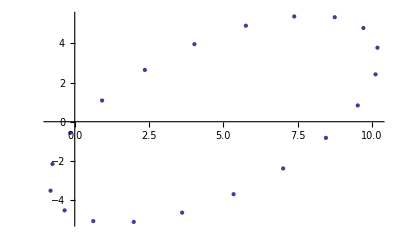
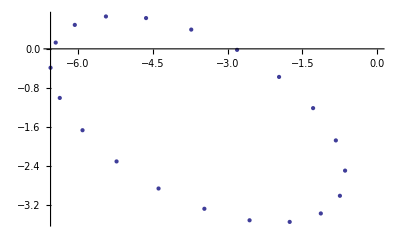
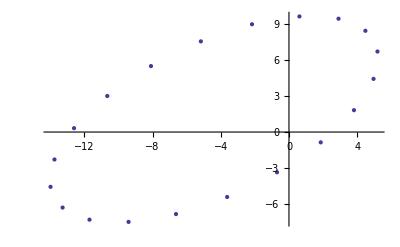
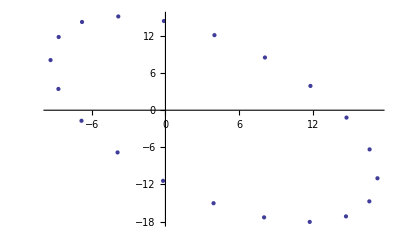
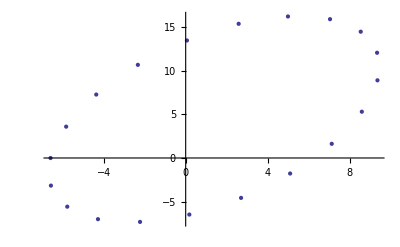
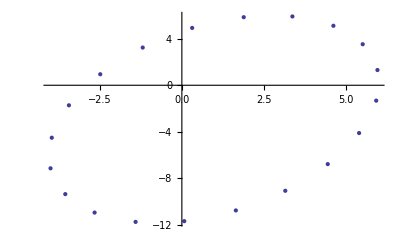

```mathematica
data=Cluster[30,20,4,2];
Table[ListPlot[data[[i]]],{i,1,Length[data]}]
```

```mathematica
Export["/home/gui/Desktop/neurodata/non-parametric-clustering/data/cluster1.dat",Cluster[30,20,2,4],"Table"]
```

/home/gui/Desktop/neurodata/non-parametric-clustering/data/cluster1.dat

```mathematica
Export["/home/gui/Desktop/neurodata/non-parametric-clustering/data/cluster2.dat",Cluster[30,20,4,2],"Table"]
```

/home/gui/Desktop/neurodata/non-parametric-clustering/data/cluster2.dat

```mathematica
Export["/home/gui/Desktop/neurodata/non-parametric-clustering/data/cluster3.dat",Cluster[30,20,3.5,0.5],"Table"]
```

/home/gui/Desktop/neurodata/non-parametric-clustering/data/cluster3.dat

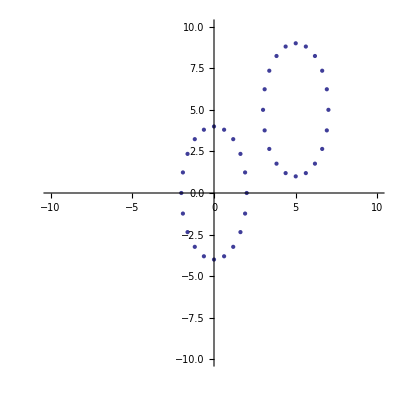

```mathematica
Show[{
ListPlot[MyEllipse[0,0,2,4,0,1,20]],
ListPlot[MyEllipse[5,5,4,2,Pi/2,1,20]]
},
AspectRatio->1,
PlotRange->{{-10,10},{-10,10}}
]
```